1.6

1.2

{0.856013,2.14003}

{4.8,0}

{5.65601,2.14003}

{RGBColor[0.5, 0, 0.5],Parallelogram[{0,0},{{1.2,0},{2,4.5}}]}

{RGBColor[0.5, 0, 0.5],Parallelogram[{1.6,0},{{1.2,0},{2,4.5}}]}

{RGBColor[0.5, 0, 0.5],Parallelogram[{3.2,0},{{1.2,0},{2,4.5}}]}

{RGBColor[0.5, 0, 0.5],Parallelogram[{4.8,0},{{4.5,0},{0.4,1}}]}

{RGBColor[0.5, 0, 0.5],Parallelogram[{5.45601,1.64003},{{4.5,0},{0.4,1}}]}

{RGBColor[0.5, 0, 0.5],Parallelogram[{6.51203,4.28007},{{4.5,0},{0.4,1}}]}

{RGBColor[0.5, 0, 0.5],Text[Western Engineering,{5,-1}]}

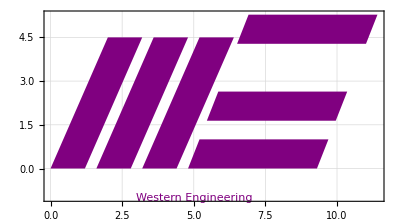

{RGBColor[0.5, 0, 0.5],Text[Western Engineering,{4,-1}]}

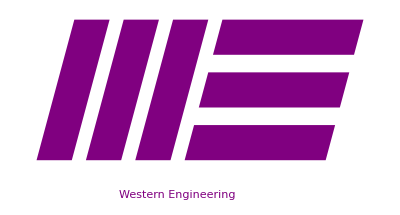

```mathematica
vertBarStep = 1.6
bt = 1.2

a = Normalize[{.4,1}]*Sqrt[1+4.5^2]/2
b = {vertBarStep*3, 0}
a+b

vertBar0 = {Purple, Parallelogram[{0,0},{{bt,0},{2,4.5}}]}
vertBar1 = {Purple, Parallelogram[{vertBarStep*1,0},{{bt,0},{2,4.5}}]}
vertBar2 = {Purple, Parallelogram[{vertBarStep*2,0},{{bt,0},{2,4.5}}]}
horizBar0 = {Purple, Parallelogram[{vertBarStep*3,0}, {{4.5, 0}, {.4,1}}]}
horizBar1 = {Purple, Parallelogram[{vertBarStep*3,0}+Normalize[{.4,1}]*(Sqrt[1+4.5^2]/2- Sqrt[1+.4^2]/2), {{4.5, 0}, {.4,1}}]}
horizBar2 = {Purple, Parallelogram[{vertBarStep*3,0}+Normalize[{.4,1}]*(Sqrt[1 + 4.5^2] ), {{4.5, 0}, {.4,1}}]}
WE = {Purple, Text[Style["Western Engineering", Large],{5, -1}]}

Graphics[Join[vertBar0, vertBar1, vertBar2, horizBar0, horizBar1, horizBar2, WE], GridLines->Automatic, Frame->True]

xStep = 1.4;
barLength = 4;
barWidth = 1;
vb0 = {Purple, Rectangle[{xStep*0, 0},{xStep*0+barWidth, barLength}]};
vb1 = {Purple, Rectangle[{xStep*1, 0},{xStep*1+barWidth, barLength}]};
vb2 = {Purple, Rectangle[{xStep*2, 0},{xStep*2+barWidth, barLength}]};
hb0 = {Purple, Rectangle[{xStep*3, 0}, {xStep*3+barLength, barWidth}]};
hb1 = {Purple, Rectangle[{xStep*3, (barLength-barWidth)/2}, {xStep*3+barLength, (barLength+barWidth)/2}]};
hb2 = {Purple, Rectangle[{xStep*3, barLength-barWidth}, {xStep*3+barLength, barLength}]};
WE = {Purple, Text[Style["Western Engineering", Large],{4, -1}]}
Logo = {GeometricTransformation[Join[vb0,vb1,vb2, hb0, hb1, hb2], ShearingTransform[15 Degree, {1,0}, {0,1}]]};
Graphics[Join[Logo, WE]]
```

```mathematica
v
```